```mathematica
ϵ=0.001
```

0.001

```mathematica
v[x_]:=Piecewise[{{ϵ+Exp[-1/(1-x^2)],x<1},{ϵ,x>1}}]
```

```mathematica
mu[x_]:=Log[x v[x]]
```

```mathematica
f[x_]:=NIntegrate[mu[s],{s,.1,x}]
```

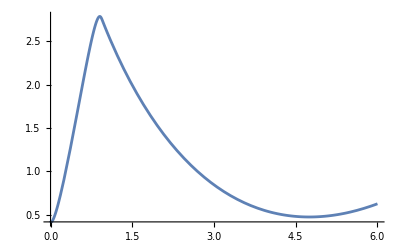

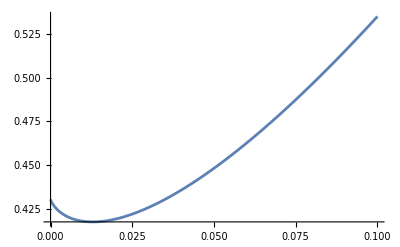

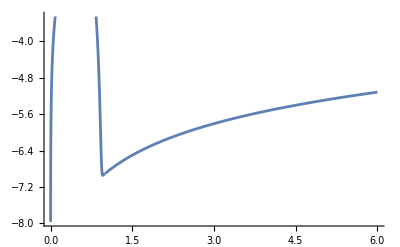

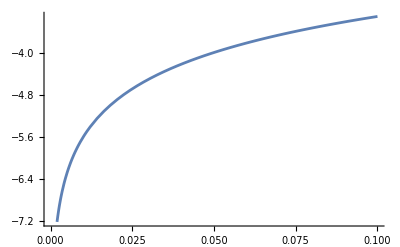

```mathematica
Plot[f[x]+5.35*x,{x,0,6}]
Plot[f[x]+5.35*x,{x,0,.1}]
Plot[Log[x v[x]],{x,0,6}]
Plot[Log[x v[x]],{x,0,.1}]
```

```mathematica
muq[x_]:=NIntegrate[v[s]^2+v[s]s v'[s],{s,0,x}]
```

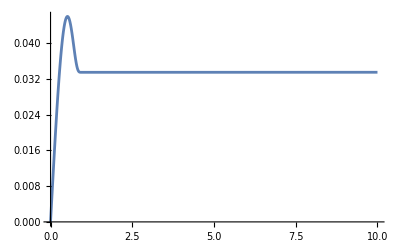

```mathematica
Plot[muq[x],{x,0,10},PlotRange->All]
```